```mathematica
<<NMRprocess`
```

NMRprocess
Version 2.1.1 2015-6-28

FourierShift::shdw: Symbol "FourierShift" appears in multiple contexts {"NMRprocess`", "Global`"}; definitions in context "NMRprocess`" may shadow or be shadowed by other definitions.

BaseLineCorrect::shdw: Symbol "BaseLineCorrect" appears in multiple contexts {"NMRprocess`", "Global`"}; definitions in context "NMRprocess`" may shadow or be shadowed by other definitions.

NMRprocess
Version 2.1.1 2015-6-28

```mathematica
ser=ReadBrukerFid[NotebookDirectory[]<>"ser",4096];
```

```mathematica
Dimensions[ser]
```

{256,4096}

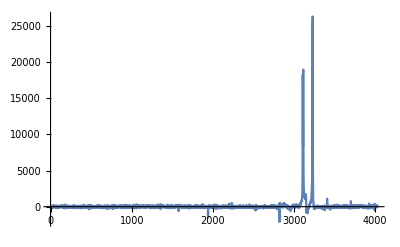

```mathematica
ListLinePlot[BaseLineCorrect@Re@NMRprocess1D[ser[[4]],LeftShift->67,Apodize->4000,Phase0->1-Pi],PlotRange->All]
```

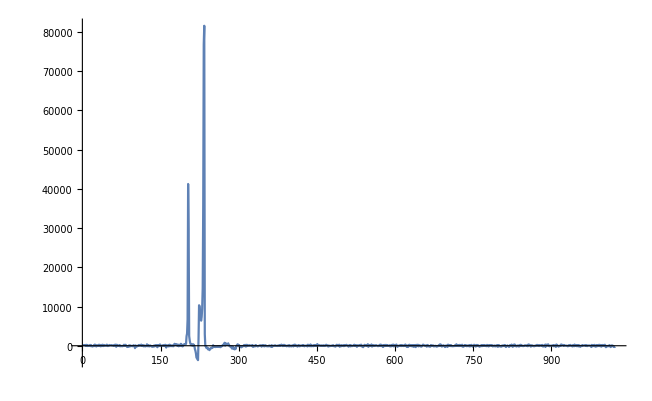

```mathematica
ListLinePlot[Reverse@BaseLineCorrect@FourierShift@Re[Fourier[PadRight[Drop[ser[[5]],67],1024]] Exp[-2.4I]],PlotRange->All]
```

```mathematica
StatesFFT[data_,OptionsPattern[{SI1->1024,SI2->1024,Phase1->0,Phase2->0,LeftShift->67}]] := Module[
	{sf2,sfa,sfb,si2=OptionValue[SI2],si1=OptionValue[SI1],
		p2=OptionValue[Phase2],p1=OptionValue[Phase1],
		ls=OptionValue[LeftShift],ser=data,apod2,apod1,n,m},

	{n,m}=Dimensions[ser];
	ser[[;;,1]] *= 0.2;
	apod2=Table[0.5+0.5 Cos[π k / si2],{k,1,si2}]; 
	sf2=Table[Reverse@BaseLineCorrect[FourierShift@Re[Fourier[apod2*PadRight[Drop[fid,ls],si2]] Exp[I p2]],
						Regions->32],{fid,ser}];
	sfa = Transpose[sf2[[1;; ;;2]] - I sf2[[2;; ;;2]]] ;
	
	sfa[[;;,1]]*=0.5;
	
	apod1= PadRight[Table[Cos[π k / n],{k,1,n/2}],si1]; 
	sfb = Table[Reverse@Re[Fourier[apod1*PadRight[fid,si1]] Exp[I p1]],{fid,sfa}];

	Transpose[sfb]
]
```

```mathematica
spect=StatesFFT[ser,Phase2->-2.25,Phase1->-0.5,SI1->512,SI2->2048];
```

Spectral width: 20 ppm x 90 ppm

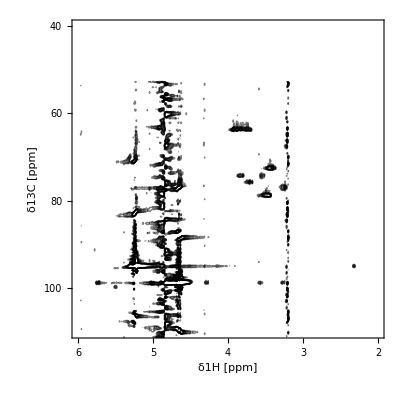

```mathematica
conts=ListContourPlot[spect /1000.,Contours->0.1Range[2,10],ContourStyle->Medium,ContourShading->None,MaxPlotPoints->Automatic,PerformanceGoal->"Precision",PlotRange->{{-6,-2},{-110,-40},All},DataRange->{{-10,10}+0.8,{-45,-45}-96.6},FrameTicks->{{Charting`ScaledTicks[{-#1&,-#1&}],Charting`ScaledFrameTicks[{-#1&,-#1&}]},{Charting`ScaledTicks[{-#1&,-#1&}],Charting`ScaledFrameTicks[{-#1&,-#1&}]}},FrameLabel->{"δ1H [ppm]","δ13C [ppm]"}]
```

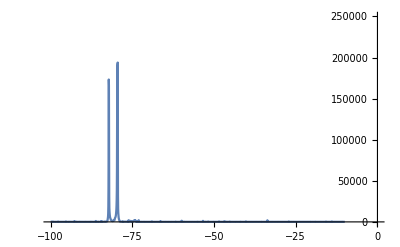

```mathematica
ListLinePlot[Table[Max[f],{f,Transpose[spect[[1;;512,;;]] ]}],PlotRange->{0,250000} ,DataRange->{-10,-100},Ticks->{Charting`ScaledTicks[{-#1&,-#1&}],Automatic},Axes->{True,False}]
```

Here is a trace through one of the anomeric 
peaks:

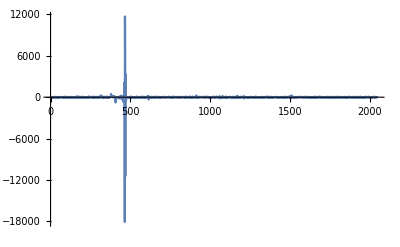

```mathematica
ListLinePlot[spect[[242]],PlotRange->All]
```

And here is the noise in the same trace: 
The SNR is of the order of 40000!

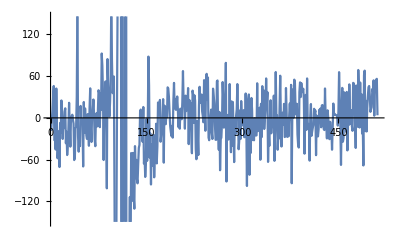

```mathematica
ListLinePlot[spect[[244]],PlotRange->Automatic]
```

Here is a trace through one of the natural abundance peaks:
SNR is still about 50!

```mathematica
Manipulate[ListLinePlot[spect[[k]],PlotRange->{-1000,10000}],{k,1,512}]
```

Part::pkspec1: The expression 5.5 cannot be used as a part specification.

ListLinePlot::lpn: {{16.8214, 18.8631, 8.32701, -3.28367, -8.96643, 8.17192, 4.51853, « 37 », -31.9117, 41.4112, -38.2534, 1.33079, 5.71623, 35.2961, « 1997 »}, « 49 », « 462 »} ⟦ 5.5 ⟧ is not a list of numbers or pairs of numbers.

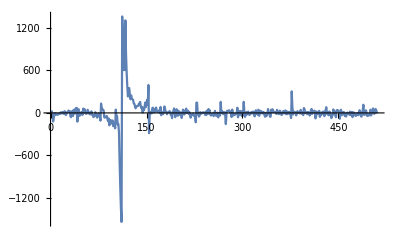

```mathematica
ListLinePlot[spect[[116]],PlotRange->All]
```

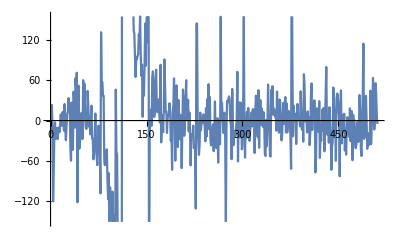

```mathematica
ListLinePlot[spect[[116]],PlotRange->Automatic]
```